## How To Use

### In order to correctly reproduce the simulations presented throughout the paper, we suggest using Interactive Epithelium (IEp) in parallel with this notebook, since some of the plots are only achievable after data storage from simulations in IEp. When needed, a message in light blue will prompt the user to run a specific model in IEp, which needs to be loaded first. In order to load models in IEp, simply load the text files in \InteractiveEpithelium\Models corresponding to the different figures (‘Model[Figurelabel].txt’). For accurate performance, we recommend running each code section in the order that they are presented here. We used Wolfram Mathematica 13. Any other version is not guaranteed to accurately reproduce the results. Figures that did not require any computation are not shown here. Note that some results are averaged over multiple simulations.

## Simulations & Figures

### Preliminary Code

```mathematica
figureFn[frameout_,i_]:=Drop[Drop[frameout[[1,1,1,1,1,i,2,1]],1],-2]//Graphics;
```

```mathematica
Om=Function[{omJ,omP,eps,npJ,npP,q,p},
np=Join[npJ,npP];
sJ=FullSimplify@Sum[omJ[i]E^(2Pi I(q i[[1]]+p i[[2]])),{i,np}];
sP=FullSimplify@Sum[omP[i]E^(2Pi I(q i[[1]]+p i[[2]])),{i,np}];
(1-eps)sJ+eps sP
];
```

```mathematica
(* MINIMIZING FUNCTIONS *)
minf=Function[{Omf,eps},NMinimize[{Omf[eps,q,p],0<q<1&&0<p<1},{q,p},Method->"RandomSearch"]];
pltmin=Function[{Omf,eps0},
er=10;
eps=Rationalize@eps0;
{min,arg}=minf[Omf,eps];
sol=DeleteDuplicates[Select[(FindRoot[{D[Omf[eps,q,p],p]==0,D[Omf[eps,q,p],q]==0},{{q,#[[1]]},{p,#[[2]]}},WorkingPrecision->25]&/@Flatten[Outer[{#1,#2}&,Range[0,1,1/10],Range[0,1,1/10]],1]),(Omf[eps,q,p]/. #)<N[Round[min,10^(-er)]-Sign[min]10^(-er)] &]/. x_?NumericQ:>Round[x,10.^-35]];
Show[Plot3D[Omf[eps,q,p],{q,0,1},{p,0,1},PlotStyle->Opacity[0.4],ClippingStyle->None,PlotRange->{{0,1},{0,1},{-0.5,1}}(*,PlotLabel->StringForm[(*"Om_min = `2`\n"<>*)"eps = `1`",N[eps],min]*),AxesLabel->{Style[StringForm["``",OverBar[q]],17],Style[StringForm["``",OverBar[p]],17]}],Graphics3D[{Red,AbsolutePointSize[6],Point[{q,p,Omf[eps,q,p]}/. sol]}]]
];
```

```mathematica
(* VIDEO AND DATA *)
vidata=Function[{Omf0,fp},
Clear[q,p];
minl={};qpl={};pltl={};
epsl=Range[0,1,N@1/fp];
epsl=ReplacePart[epsl,{Position[epsl,0.7000000000000001]->0.7}];
Do[
AppendTo[pltl,pltmin[Omf0,ei]];
AppendTo[minl,min];
AppendTo[qpl,{q,p}/. sol],
{ei,epsl}];
exampleFrames=pltl;
rasterizedFrames=Map[Image,exampleFrames];
ListAnimate[rasterizedFrames,ControlPlacement->Top]];
```

```mathematica
(* MINIMISATION PLOTS *)
minplot=Function[{},
ListLinePlot[Transpose[{epsl,1/Abs@minl}],AxesLabel->{"ϵ"},Frame->True,PlotRange->{{0,1},Automatic},FrameLabel->{"ϵ","1/|Ω_min|"},LabelStyle->18,AspectRatio->2/3]];
```

```mathematica
(* FOURIER MODES PLOTS *)
modplot=Function[{},
qpln=Select[#,0<#[[1]]<1&&0<#[[2]]<1&]&/@qpl;
qpa=AssociationThread[epsl,qpln];
ql=Table[#[[1]]&/@qpln[[j]],{j,Length@qpln}];
pl=Table[#[[2]]&/@qpln[[j]],{j,Length@qpln}];
ListPlot[{Flatten[Table[{epsl[[j]],#}&/@pl[[j]],{j,Length@epsl}],1],(#-{0,0.01})&/@Flatten[Table[{epsl[[j]],#}&/@ql[[j]],{j,Length@epsl}],1]},AxesLabel->{"ϵ"},PlotStyle->{Purple,Orange}
,Frame->True,PlotRange->{{0,1},Automatic},FrameLabel->{"ϵ",StringForm["Fourier modes (`1`,`2`)",OverBar[q],OverBar[p]]}
,PlotLegends->Placed[{StringForm["``",OverBar[q]],StringForm["``",OverBar[p]]},{.1,.15}],LabelStyle->18,AspectRatio->2/3]];
```

```mathematica
(* MULTIPLE MINIMA *)
OmfR20[eps_,q_,p_]:=(1/3) (1-eps) (Cos[2 p π]+Cos[2 π q]+Cos[2 π (p+q)])+(1/6) eps (Cos[4 p π]+Cos[2 π (p-q)]+Cos[4 π q]+Cos[4 π (p+q)]+Cos[2 π (2 p+q)]+Cos[2 π (p+2 q)]);
```

```mathematica
vidata[OmfR20,200]//Quiet;
```

```mathematica
(* TEMPORAL EIGENVALUE FUNCTION *)
lampf=Function[{Omf,eps,ab,nu,sg,q,p},
(1/2)*(-1*(1+nu)+sg Sqrt[(1+nu)^2-4nu(1-ab Omf[eps,q,p])])];
lampfm=Function[{Omf,eps,ab,nu,sg,q,p},
(1/2)*(-1*(1+nu)+sg Sqrt[(1+nu)^2-4nu(1-1)])];
```

```mathematica
rootf=Function[{a,b,h},
N@Root[-1+(1+a^5) #1+4 a^4 b #1^(h+1)+6 a^3 b^2 #1^(2h+1)+4 a^2 b^3 #1^(3h+1)+a b^4 #1^(4h+1)&,1]];
```

```mathematica
fn[x_,a_,b_,h_]:=x^h/(a+x^h)
gn[x_,a_,b_,h_]:=1/(1+b x^h)
ABf=Function[{a,b,h},
n0=N@rootf[a,b,h];
A=(a h (gn[n0,a,b,h])^(h-1))/(a+(gn[n0,a,b,h])^h)^2;
B=-(h b (n0)^(h-1))/(1+b(n0)^h)^2;
N[A*B]
];
```

```mathematica
Omina=AssociationThread[epsl,minl];
```

```mathematica
rootf=Function[{a,b,h},
N@Root[a #1+(-1+#1) (1+b #1^h)^(-h)&,1]];
```

```mathematica
rootf=Function[{a,b,h},
N@Root[1-#1-a/(a+(1/(1+b #1^h))^h)&,1]];
```

```mathematica
fn=Function[{x,a,b,h},((x^h)/(a+x^h))];
gn=Function[{x,a,b,h},(1/(1+b x^h))];
ABf=Function[{a,b,h},
n0=N@rootf[a,b,h];
A=(a h (1/(1+b n0^h))^(-1+h))/((a+(1/(1+b n0^h))^h)^2);
B=-(b h n0^(-1+h))/((1+b n0^h)^2);
N[A*B]
];
ABf2=Function[{a,b,h},
n0=N@rootf[a,b,h];
-N[(n0^(1-h)gn[n0,a,b,h]^(1-h)((1+b n0^h)(a+gn[n0,a,b,h]^h))^2)/(a b h h)]
];
```

```mathematica
(* HEXAGONAL INDEX FUNCTION *)
hindf=Function[k,
indl={{0,0}};
indl0={};
suml=Table[ij,{ij,{{0,1},{1,1},{1,0},{0,-1},{-1,-1},{-1,0}}}];
Do[
indl0=Join[indl0,indl];
indl=Complement[Flatten[Table[indl[[j]]+#&/@suml,{j,Length@indl}],1],indl0],
k];
indl
];
```

```mathematica
Clear[omJ,omP,eps,npJ,npP,q,p,pll,ds,sig1];
pll=4;ds=2;
npJ=hindf[1];
npP=Flatten[Table[hindf[i],{i,2,pll}],1];
dsa=Merge[Table[AssociationThread[hindf[j],ConstantArray[j,Length@hindf[j]]],{j,2,pll}],Total];
omJ[npt_]:=If[MemberQ[npJ,npt],1/6,0];
omP=Function[{npt,sig1},
ws=1/(Sum[E^(-sig1(dsa[ij]-ds)^2),{ij,npP}]);
If[MemberQ[npP,npt],
ws*E^(-sig1 (dsa[npt]-ds)^2)
,0]];
```

```mathematica
(* MULTIPLE MINIMA - pll = 4 *)
OmfRL0[eps_,q_,p_,sig_]:=1/(6 (4+ⅇ^(3 sig) (3+2 ⅇ^sig)))ⅇ^(-8 ⅈ π (p+q)) (1+ⅇ^(2 ⅈ p π)+ⅇ^(4 ⅈ p π)+ⅇ^(6 ⅈ p π)+ⅇ^(8 ⅈ p π)+ⅇ^(2 ⅈ π q)+ⅇ^(4 ⅈ π q)+ⅇ^(6 ⅈ π q)+ⅇ^(8 ⅈ π q)+ⅇ^(16 ⅈ π (p+q))+ⅇ^(8 ⅈ π (2 p+q))+ⅇ^(4 ⅈ π (3 p+q))+ⅇ^(2 ⅈ π (5 p+q))+ⅇ^(8 ⅈ π (p+2 q))+ⅇ^(4 ⅈ π (p+3 q))+ⅇ^(4 ⅈ π (4 p+3 q))+ⅇ^(2 ⅈ π (7 p+3 q))+ⅇ^(4 ⅈ π (3 p+4 q))+ⅇ^(2 ⅈ π (p+5 q))+ⅇ^(2 ⅈ π (8 p+5 q))+ⅇ^(2 ⅈ π (3 p+7 q))+ⅇ^(2 ⅈ π (8 p+7 q))+ⅇ^(2 ⅈ π (5 p+8 q))+ⅇ^(2 ⅈ π (7 p+8 q))+ⅇ^(4 ⅈ π (p+q)+4 sig) (1+ⅇ^(2 ⅈ p π)+ⅇ^(4 ⅈ p π)+ⅇ^(2 ⅈ π q)+ⅇ^(4 ⅈ π q)+ⅇ^(8 ⅈ π (p+q))+ⅇ^(4 ⅈ π (2 p+q))+ⅇ^(2 ⅈ π (3 p+q))+ⅇ^(4 ⅈ π (p+2 q))+ⅇ^(2 ⅈ π (p+3 q))+ⅇ^(2 ⅈ π (4 p+3 q))+ⅇ^(2 ⅈ π (3 p+4 q)))+ⅇ^(2 ⅈ π (p+q)+3 sig) (1+ⅇ^(2 ⅈ p π)+ⅇ^(4 ⅈ p π)+ⅇ^(6 ⅈ p π)+ⅇ^(2 ⅈ π q)+ⅇ^(4 ⅈ π q)+ⅇ^(6 ⅈ π q)+ⅇ^(12 ⅈ π (p+q))+ⅇ^(6 ⅈ π (2 p+q))+ⅇ^(2 ⅈ π (4 p+q))+ⅇ^(6 ⅈ π (p+2 q))+ⅇ^(4 ⅈ π (3 p+2 q))+ⅇ^(2 ⅈ π (5 p+2 q))+ⅇ^(4 ⅈ π (2 p+3 q))+ⅇ^(2 ⅈ π (p+4 q))+ⅇ^(2 ⅈ π (2 p+5 q))+ⅇ^(2 ⅈ π (6 p+5 q))+ⅇ^(2 ⅈ π (5 p+6 q)))) eps+1/3 (1-eps) (Cos[2 p π]+Cos[2 π q]+Cos[2 π (p+q)])
```

```mathematica
(* MINIMIZING FUNCTIONS *)
minfG=Function[{Omf,eps,sig},NMinimize[{Re@Omf[eps,q,p,sig],0<q<1&&0<p<1},{q,p},Method->"RandomSearch"]];
pltminG=Function[{Omf,eps0,sig},
er=10;
eps=Rationalize@eps0;
{min,arg}=minfG[Omf,eps,sig];
sol=DeleteDuplicates[Select[(FindRoot[{D[Omf[eps,q,p,sig],p]==0,D[Omf[eps,q,p,sig],q]==0},{{q,#[[1]]},{p,#[[2]]}},WorkingPrecision->MachinePrecision]&/@Flatten[Outer[{#1,#2}&,Range[0,1,1/10],Range[0,1,1/10]],1]),(Re@Omf[eps,q,p,sig]/. #)<N[Round[min,10^(-er)]-Sign[min]10^(-er)] &]/. x_?NumericQ:>Round[x,10.^-35]];

Show[Plot3D[Re@Omf[eps,q,p,sig],{q,0,1},{p,0,1},PlotStyle->Opacity[0.4],ClippingStyle->None,PlotRange->{{0,1},{0,1},{-0.5,1}}(*,PlotLabel->StringForm[(*"Om_min = `2`\n"<>*)"eps = `1`",N[eps],min]*),Exclusions->None,AxesLabel->{Style[StringForm["``",OverBar[q]],17],Style[StringForm["``",OverBar[p]],17]}],Graphics3D[{Red,AbsolutePointSize[6],Point[{q,p,Omf[eps,q,p,sig]}/. sol]}]]
];
```

```mathematica
(* VIDEO AND DATA *)
vidataG=Function[{Omf0,sig,fp},
Clear[q,p];
minl={};qpl={};pltl={};
epsl=Range[0,1,N@1/fp];
Do[
AppendTo[pltl,pltminG[Omf0,ei,sig]];
AppendTo[minl,min];
AppendTo[qpl,{q,p}/. sol],
{ei,epsl}];
exampleFrames=pltl;
rasterizedFrames=Map[Image,exampleFrames];
ListAnimate[rasterizedFrames,ControlPlacement->Top]];
```

```mathematica
minplotG=Function[{Omf,sigl,fp},
Clear[q,p];
minlT={};
Do[
minl={};qpl={};pltl={};
epsl=Range[0,1,N@1/fp];
Do[
AppendTo[pltl,pltminG[Omf,ei,sig]];
AppendTo[minl,min];
AppendTo[qpl,{q,p}/. sol];
PrintTemporary[StringForm["`1` - `2`",sig,ei]],
{ei,epsl}];
minlT=Append[minlT,minl],
{sig,sigl}];
ListLinePlot[Table[Transpose[{epsl,1/Abs@minlT[[j]]}],{j,Length@minlT}],AxesLabel->{"ϵ"}(*,PlotLabel->"Om_min"*),PlotLegends->Placed[Table[StringForm["σ_1 = ``",sigl[[j]]],{j,Length@minlT}],{.1,.75}]
,ImageSize->550,Frame->True,PlotRange->{{0,1},Automatic},FrameLabel->{Style["ϵ",20],Style["|AB|",20]},LabelStyle->17]
];
```

```mathematica
pattern0=Function[{n,m,eps,qpll,Cqp},
hexa=Association[Sequence@@Flatten[Table[{j,k}->Translate[RegularPolygon[6],{3/2j,-Sqrt[3]/2j+Sqrt[3]k}],{j,n},{k,m}],1]];
ttb=Chop@Table[
Re@Sum[Cqp[qpli]E^(2Pi I (qpli[[1]] j+qpli[[2]] k)),{qpli,qpll}],{j,n},{k,m}];
solr=1-Rescale[ttb];
Graphics[Table[{RGBColor[0.357,0.667,0.196,solr[[j,k]]],EdgeForm[Black],hexa[{j,k}]},{j,n},{k,m}]]];
```

```mathematica
pselection=Function[eps,
n=m=2LCM[Sequence@@Flatten[(1/(Rationalize[#,0.01]&/@qpa[N@eps]))]];
If[n>30,n=m=14,n=m=14];
n=m=14;
cl=ConstantArray[1,Length@qpa[N@eps]];
(*
Supplementary figures: Tweak for custom constants and multiple cell types;
cl={1,0.7I};
cl={1,0,1,1,1,0,1,1};
cl={-1,-1,-1,-1,-1,-1};
*)
Cqp=AssociationThread[qpa[N@eps]->cl];

gplt=Quiet[Grid[Transpose[Join[{pattern0[n,m,eps,{#},KeyTake[Cqp,{#}]],First@Rationalize[{#},0.01]}&/@(qpa[N@eps][[1;;Length@qpa[N@eps]/2]]),
{{"⟶",""},{pattern0[n,m,eps,qpa[N@eps][[1;;Length@qpa[N@eps]]],Cqp],""}}]],Spacings->{0.2,0}]];
gplt2=Quiet[Grid[Transpose[Join[{Show[pattern0[n,m,eps,{#},KeyTake[Cqp,{#}]],Graphics[Text[Style[StringForm["``",First@Rationalize[{#},0.01]],22],{6,-9}]]]}&/@(qpa[N@eps][[1;;Length@qpa[N@eps]/2]]),
{{"⟶"},{pattern0[n,m,eps,qpa[N@eps][[1;;Length@qpa[N@eps]]],Cqp]}}]],Spacings->{0.2,0}]];
Rasterize[gplt2,RasterSize->1920]];
```

```mathematica
qpt=N@{{1/7,1/7},{6/7,6/7}};
pselection2=Function[eps,
n=m=2LCM[Sequence@@Flatten[(1/(Rationalize[#,0.01]&/@qpt))]];
If[n>30,n=m=14,n=m=14];
n=m=14;
cl=ConstantArray[1,Length@qpt];
(*
Supplementary figures: Tweak for custom constants and multiple cell types;
cl={1,0.7I};
cl={1,0,1,1,1,0,1,1};
cl={-1,-1,-1,-1,-1,-1};
*)
Cqp=AssociationThread[qpt->cl];

gplt=Quiet[Grid[Transpose[Join[{pattern0[n,m,eps,{#},KeyTake[Cqp,{#}]],First@Rationalize[{#},0.01]}&/@(qpt[[1;;Length@qpt/2]]),
{{"⟶",""},{pattern0[n,m,eps,qpt[[1;;Length@qpt]],Cqp],""}}]],Spacings->{0.2,0}]];
gplt2=Quiet[Grid[Transpose[Join[{Show[pattern0[n,m,eps,{#},KeyTake[Cqp,{#}]],Graphics[Text[Style[StringForm["``",First@Rationalize[{#},0.01]],22],{6,-9}]]]}&/@(qpt[[1;;Length@qpt/2]]),
{{"⟶"},{pattern0[n,m,eps,qpt[[1;;Length@qpt]],Cqp]}}]],Spacings->{0.2,0}]];
Rasterize[gplt2,RasterSize->1920]];
```

### Figure 1

#### Figure 1 (a)

```mathematica
Ftorus[t_,u_,r_]:={Cos[t],Sin[t],Sin[# u]/#} #^2/(r-Cos[# u])&[Sqrt[r^2-1]]
Pfast[r_,m_,n_]:=Graphics3D[GraphicsComplex[Flatten[Table[Ftorus[2. Pi (i+k/3.)/n,Pi (1.+i+2 j)/m/Sqrt[r^2-1.],r//N],{j,m},{i,n},{k,{-1,+1}}],2],Polygon[Join@@Table[Mod[(j-1) (2 n)+{1,2,3+If[i==n,n (n-2),0]}~Join~({2,1,If[i==1,n (2-n),0]}+2 n)+2 (i-1),2 n m,1],{i,n},{j,m}]]],Boxed->False];
Pfast[3.5,10,34]
(* Followed by colour adjustment *)
```

#### Figure 1 (c)

Run ‘Model1c’ in IEp

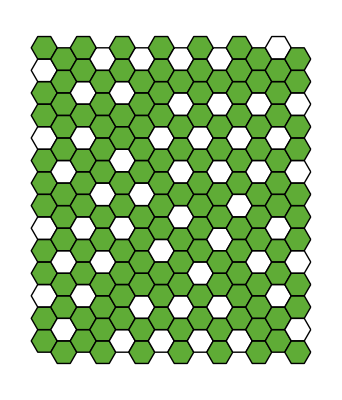

```mathematica
figureFn[frameout,-1]
```

#### Figure 1 (d)

Run ‘Model1d’ in IEp

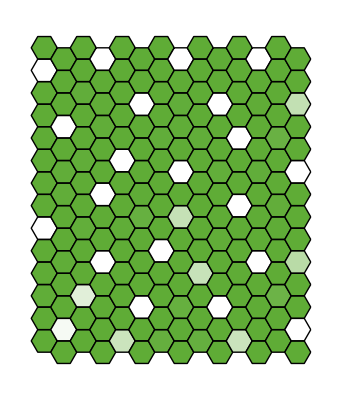

```mathematica
figureFn[frameout,-1]
```

#### Figure 1 (e)

Run ‘Model1e’ in IEp

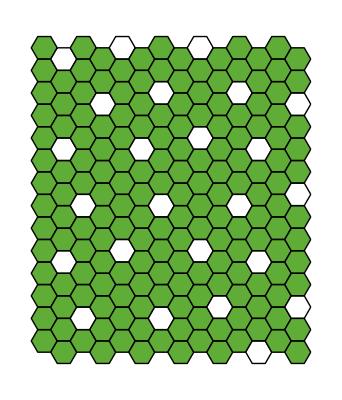

```mathematica
figureFn[frameout,-1]
```

#### Figure 1 (f)

Run ‘Model1f’ in IEp

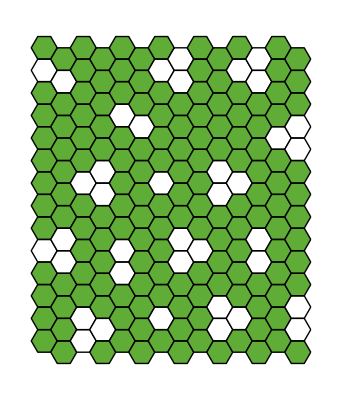

```mathematica
figureFn[frameout,-1]
```

#### Scale bar

```mathematica
Graphics[{LinearGradientFilling[{RGBColor[{94,172,54}/255],White},Pi/2],Rectangle[{0,0},{1,5}],Text[Style["0",13],{1.4,0}],Text[Style["1",13],{1.4,5}],Rotate[Text[Style["Delta level",13],{-0.5,2.5}],Pi/2]},ImageSize->Tiny]
```

### Figure 2

#### Figure 2 (a)

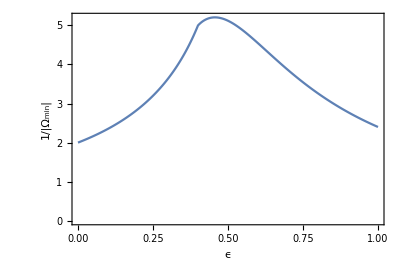

```mathematica
minplot[]
```

#### Figure 2 (b)

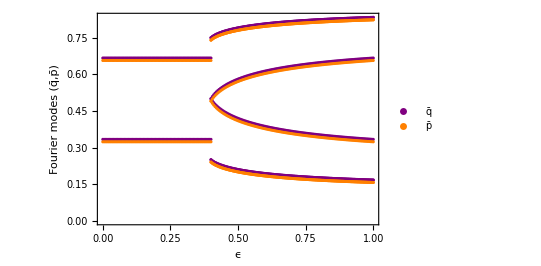

```mathematica
modplot[]
```

#### Figure 2 (c)

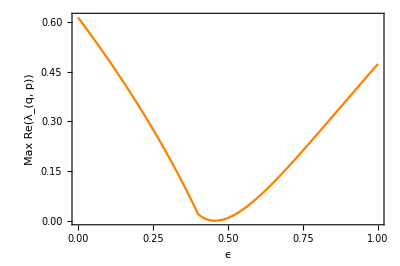

```mathematica
(* MAXIMISATION OF RE(λ) *)
maxl=Table[{ep,NMaximize[{Re@lampf[OmfR20,ep,1/Max[minl],1,1,q,p],0<q<1&&0<p<1},{q,p},Method->"RandomSearch"][[1]]},{ep,epsl}];
ListLinePlot[maxl,AxesLabel->{"ϵ"},PlotStyle->Orange,Frame->True,PlotRange->{{0,1},Automatic},FrameLabel->{"ϵ","Max Re(λ_(q, p))"},LabelStyle->18,AspectRatio->2/3]
```

#### Figures 2 (d-f)

```mathematica
Grid[{{pltmin[OmfR20,0.2],pltmin[OmfR20,.4],pltmin[OmfR20,.6]}}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-

#### Figures 2 (g-i)

Run ‘Model2g’, ‘Model2h’ and ‘Model2i’ in IEp

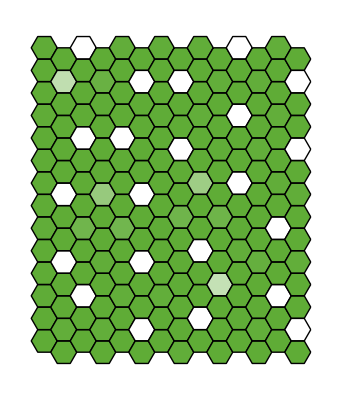

```mathematica
(* 'Model2g' *)
figureFn[frameout,-1]
```

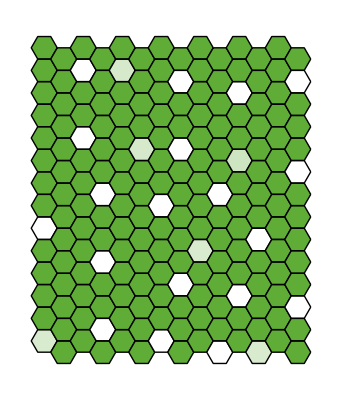

```mathematica
(* 'Model2h' *)
figureFn[frameout,-1]
```

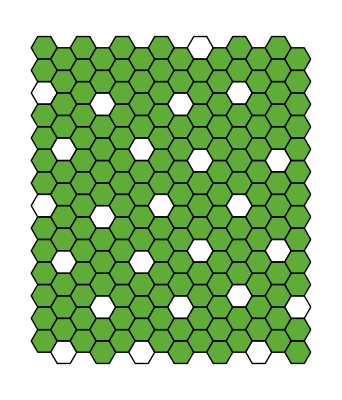

```mathematica
(* 'Model2i' *)
figureFn[frameout,-1]
```

### Figure 3

```mathematica
(* Uncomment for animation of contour plots *)
(*
h0=6;
Manipulate[Show[RegionPlot[ABf[1/10^rt,10^b,h0]<1/Omina[eps],{rt,-1,6},{b,0,2},AspectRatio->1/2,FrameLabel->{"log_10 r_t","log_10 b"}]],
{eps,0.,1.,0.005,Appearance->"Labeled"}]
*)
```

{-11.9859,{rt→4.04124,b→2.}}

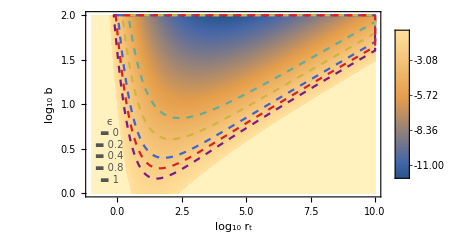
-Graphics-
-Graphics-

```mathematica
h0=6;Clear[b];
rtmin=-1;
rtmax=10;
NMinimize[{ABf[1/10^rt,10^b,h0],rtmin<=rt<=rtmax&&0<=b<=2},{rt,b}]
pnt[eps_]:=RegionPlot[ABf[1/(10^rt),10^b,h0]<1/Omina[eps],{rt,rtmin,rtmax},{b,0,2},AspectRatio->1/2,FrameLabel->{"log_10 r_t","log_10 b"},BoundaryStyle->{ColorData["Rainbow"][eps],Dashed},PlotStyle->Transparent]
cnt=ContourPlot[ABf[1/10^rt,10^b,h0],{rt,rtmin,rtmax},{b,0,2},AspectRatio->3.5/6,PlotLegends->
Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendMarkerSize->{40,170},LabelStyle->{FontFamily->"Calibri",FontSize->10}],{.9,.45}],FrameLabel->{"log_10 r_t","log_10 b"},ContourStyle->None,Contours->100];
ent=RegionPlot[(10^rt)*10^b<0,{rt,rtmin,rtmax},{b,0,2},AspectRatio->1/2,FrameLabel->{"log_10 r_t","log_10 b"},BoundaryStyle->Transparent,PlotStyle->Transparent,PlotLegends->Placed[Style[StringForm["  ϵ\n`1` `2`\n`3` `4`\n`5` `6`\n`7` `8`\n`9` `10`",Sequence@@Flatten@Table[{Style["▬",ColorData["Rainbow"][eps]],StringForm["``",eps]},{eps,{0,0.2,0.4,0.8,1}}]],10,Darker@Gray,TextAlignment->Left],{.08,.25}]];
rgg2=Graphics[{Inset[Graphics[{Yellow,Text["x"]}],{4.041,2}],Inset[Graphics[{Red,Text["x"]}],{1,2}],Inset[Graphics[{Red,Text["x"]}],{2,1}],Inset[Graphics[{Red,Text["x"]}],{5,1.3}]}];
Show[cnt,pnt[0.],pnt[0.2],pnt[0.4],pnt[0.71],pnt[1.],ent,rgg2]
```

### Figure 4

#### Figure 4 (a-d)

Run ‘Model4a’, ‘Model4b’, ‘Model4c’ and ‘Model4d’ in IEp

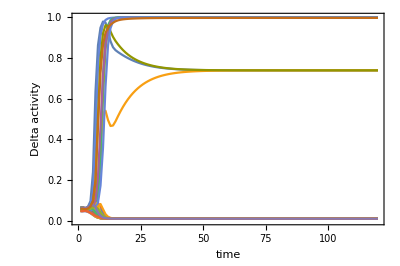

```mathematica
(* 'Model4a' *)
ListLinePlot[Table[(#[j]&/@sols[[1;;120]])[[All,2]],{j,lvs}],Frame->True,PlotRange->{0,1},AspectRatio->2/3,FrameLabel->{Style["time",20],Style["Delta activity",20]},FrameStyle->15]
```

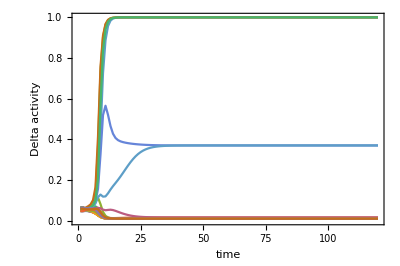

```mathematica
(* 'Model4b' *)
ListLinePlot[Table[(#[j]&/@sols[[1;;120]])[[All,2]],{j,lvs}],Frame->True,PlotRange->{0,1},AspectRatio->2/3,FrameLabel->{Style["time",20],Style["Delta activity",20]},FrameStyle->15]
```

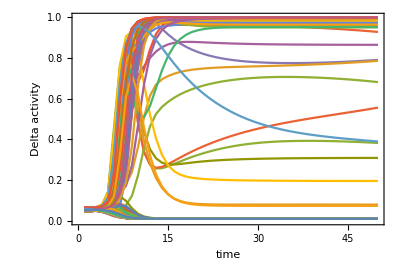

```mathematica
(* 'Model4c' *)
ListLinePlot[Table[(#[j]&/@sols[[1;;50]])[[All,2]],{j,lvs}],Frame->True,PlotRange->{0,1},AspectRatio->2/3,FrameLabel->{Style["time",20],Style["Delta activity",20]},FrameStyle->15]
```

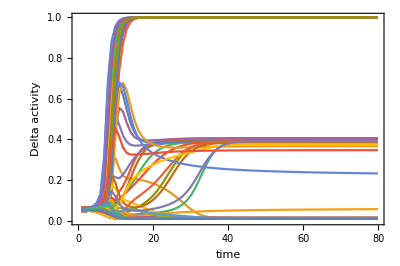

```mathematica
(* 'Model4d' *)
ListLinePlot[Table[(#[j]&/@sols[[1;;80]])[[All,2]],{j,lvs}],Frame->True,PlotRange->{0,1},AspectRatio->2/3,FrameLabel->{Style["time",20],Style["Delta activity",20]},FrameStyle->15]
```

### Figure 5

#### Figures 5 (a-c)

```mathematica
(* VIDEO AND DATA *)
vidataG[OmfRL0,0.1,200]//Quiet;
```

```mathematica
Grid[{{Quiet@pltminG[OmfRL0,0.2,0],Quiet@pltminG[OmfRL0,0.4,0],Quiet@pltminG[OmfRL0,0.6,0]}}]
```

#### Figure 5 (d)

```mathematica
minplotG[OmfRL0,{0,0.1,0.5,1,2,10},100]//Quiet
```

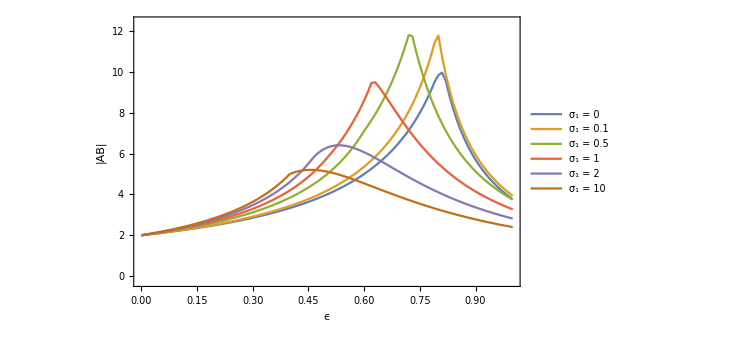

#### Figure 5 (e)

```mathematica
pll=2;
dsa=Merge[Table[AssociationThread[hindf[j],ConstantArray[j,Length@hindf[j]]],{j,2,pll}],Total];
lll=Table[
dsa=Merge[Table[AssociationThread[hindf[j],ConstantArray[j,Length@hindf[j]]],{j,2,jk}],Total];
1/Re[1/(Sum[E^(-sig1(dsa[ij]-2)^2),{ij,Flatten[Table[hindf[i],{i,2,jk}],1]}])],{jk,2,12}];
LogLogPlot[{lll[[1]],lll[[2]],lll[[3]],lll[[4]],lll[[5]],lll[[6]],lll[[7]],lll[[8]],lll[[9]],lll[[10]],lll[[11]]},{sig1,0,10},PlotRange->{{0,10},{0,300}},PlotStyle->"SolarColors",PlotLegends->Placed[Table[StringForm["p_ℓ = ``",j],{j,2,11}],{.9,0.6}],ImageSize->550,Frame->True,PlotRange->{{0,10},Automatic},FrameLabel->{Style["σ_1",20],Style["1/ω^*",20]}]
```

### Figure 6

#### Figures 6 (a-c)

Run ‘Model6a’, ‘Model6b’ and ‘Model6c’ in IEp

```mathematica
(* 'Model6a' *)
figureFn[frameout,-1]
```

```mathematica
(* 'Model6b' *)
figureFn[frameout,-1]
```

```mathematica
(* 'Model6c' *)
figureFn[frameout,-1]
```

### Figure 7

#### Data

```mathematica
e06b10d35={∞,∞,9.187793230437402*^-16,∞,∞,∞,0.31149565873711127,0.2610685465490836,0.2652026794276314,0.2302500989918336,0.23970472614236873,0.2525258467279983,0.21914100244592724,0.2279915509612189,0.2299873399622315,0.21209031602288597,0.19817514604541184,0.21492047278650547,0.2349550383660475,0.19950938709659435,0.2198851882102013,0.21058823526422388,0.20019100875813417,0.20019100875813417,0.19594146835596468,0.1965544761006431,0.19594146835596468,0.19980216569671774,0.21143102612852033,0.20019100875813417,0.20978112372030888,0.19801339978166665,0.2235538261089427,0.22385608369846116,0.21749868419016688,0.20361585752053885,0.20349043158283298,0.22030291983248046,0.21047011948963343,0.20522211784886465,0.19896373268326809,0.22071652158337016,0.20356984934320038,0.21082079585461302,0.21142114703042877,0.2159694604047936,0.21899043886658878,0.1827717095363688,0.19091285212558098,0.1894901999460457,0.19028869972855178,0.18724041973351938,0.18621953070736266,0.18621953070736266,0.19033146609616647,0.19033146609616647,0.19033146609616647,0.19033146609616647,0.19033146609616647,0.19033146609616647,0.19033146609616647,0.19033146609616647,0.1827717095363688,0.19097183231309434,0.18024781748617238,0.18024781748617238,0.18024781748617238,0.17121975913202755,0.18024781748617238,0.1660219040086208,0.1660219040086208,0.18024781748617238,0.18024781748617238,0.1878392824569815,0.18118379963106088,0.178118455227114,0.18024781748617238,0.18363552200331035,0.18024781748617238,0.18363552200331035,0.1756033733760462,0.17121975913202755,0.17121975913202755,0.17121975913202755,0.17374137577958287,0.18029584341793195,0.1802478174861724,0.1802478174861724,0.1802478174861724,0.1802478174861724,0.1667502794455707,0.18568906627104867,0.17106721503923225,0.17106721503923225,0.17106721503923225,0.17106721503923225,0.17106721503923225,0.1802478174861724,0.17898902986552578,0.16297681395907848,0.17622617443091587,0.17660904333698946,0.17660904333698946,0.17839244196339749,0.16630693045004102,0.16630693045004102,0.1743865166091226,0.18662542796182505,0.17866713625351474,0.1764276990521951,0.16952306458661112,0.16955322052289618,0.16955322052289618,0.15493973093897842,0.15608837715030513,0.15608837715030513,0.14469152109667036,0.15632632089293627,0.1741313184779406,0.19060099491965768,0.19604036372106953,0.17520019833509146,0.17520019833509146,0.18746145004905945,0.19662700763011287,0.1910991555858572,0.17157409252944344,0.17847294819016682,0.16774322717626725,0.15296462979881337,0.16364684881462685,0.17899384036800223,0.18028217827610196,0.1825798977496291,0.18855306503388905,0.18028217827610196,0.1662254974011856,0.18367585765307418,0.16364684881462682,0.1753321890663738,0.1753321890663738,0.1765012059108943,0.18666260820029798,0.1817555793680511,0.1737113300582549,0.1817555793680511,0.18119841897341346,0.19195763064913057,0.1879511401530101,0.20403832023103088,0.16836451035245897,0.2059930500151841,0.1872938990953785,0.17558231245863803,0.16911727187619988,0.17576447284923324,0.16593863793974797,0.19323322848814,0.17433073841176686,0.1799137052027877,0.19213342609639605,0.18479910036977518,0.19442019038185337,0.19913703426230742,0.18726476126064584,0.16757728297077656,0.18195140724128903,0.16745381983841978,0.18143953394848858,0.17355612813295554,0.17004559188600915,0.19502365471551172,0.16575677398556124,0.1519536883754241,0.1680718193480795,0.17710916892726408,0.19810676708725528,0.192727490133716,0.17231899278552962,0.1872363378356723,0.18241362768022631,0.16506460902728076,0.16307378664949698,0.1634368865690523,0.19891134279798778,0.1740763399730894,0.17780665825842137,0.18590474071976332,0.18094017576640628,0.19629993756278125,0.18300435194138112,0.1917651141457707,0.1917651141457707,0.18625598774164942,0.17256499382400173,0.17433073841176686,0.17433073841176686,0.15960997620064,0.16283188971920992,0.16888128564648278,0.17402232049178773,0.15297325370140424,0.15297325370140424,0.16118593799737904,0.16118593799737904,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.15297325370140424,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.15297325370140424,0.15297325370140424,0.15297325370140424,0.15297325370140424,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.1517832143143363,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.1559960685856814,0.1559960685856814,0.16896476205260522,0.1517832143143363,0.1517832143143363,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.158627032343519,0.158627032343519,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16896476205260522,0.16118593799737904,0.16118593799737904,0.1566464015886298,0.1566464015886298,0.1566464015886298,0.15866807149069928,0.15866807149069928,0.1581855765819652,0.16934270178015917,0.16934270178015917,0.15308941035427542,0.15308941035427542,0.15308941035427542,0.13359977425472536,0.15328801452175642,0.15328801452175642,0.15424402976434715,0.14343653855531896,0.14343653855531896,0.14343653855531896,0.14343653855531896,0.14343653855531896,0.14343653855531896,0.14343653855531896,0.14343653855531896,0.14343653855531896,0.14343653855531896,0.14343653855531896,0.14343653855531896,0.14343653855531896,0.14343653855531896,0.13172676875173045,0.12131930020141887,0.13501762990002192,3.826151322451242*^-16,3.826151322451242*^-16,0.08503323845003323,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16,3.826151322451242*^-16};
e02b10d35={∞,∞,9.187793230437402*^-16,∞,∞,∞,∞,0.36275978552949906,0.27750615356395286,0.2514136567803689,0.24634419667245064,0.2299414640230711,0.22072173714383667,0.22057209946551598,0.210470554021172,0.21724758427379137,0.2202836374774927,0.2139626493806354,0.21156849234996217,0.21241849232591845,0.20804348294754557,0.20821305759228942,0.20993422020246544,0.21059454107337475,0.20836989941457007,0.2095322144742432,0.2104826584706691,0.2161883974060394,0.22009286905361028,0.22314895826193587,0.21667740822825257,0.21918529485805013,0.2265676751481204,0.22626615029693575,0.22688179197463715,0.22406743023864115,0.21709534437508515,0.21332838128980217,0.21479560564407604,0.21860025315881348,0.2162555247679351,0.21047709514795784,0.21405770674470406,0.20812909862197618,0.2156537970041217,0.2081673713747316,0.2087016777689908,0.2208058827129318,0.21461468344037155,0.2131211895174105,0.21615860332268957,0.22056732857267855,0.22061588277079025,0.21536536352788177,0.21734596881906515,0.2142801636626823,0.21057185179198992,0.21358881333998392,0.21200408162107104,0.2150558264259625,0.2132670536444607,0.21346180495144396,0.21454566209597511,0.22097623975286554,0.2156702743233411,0.21651074081077967,0.20995418937067256,0.21084247958129093,0.21450693483621516,0.20519374269332255,0.2129057691914388,0.20823931181345617,0.2132586844775454,0.2069708683110817,0.2069708683110817,0.2170012491022714,0.21471738096353105,0.21670258669243112,0.2143828489580973,0.22207398576746923,0.21741067123691707,0.21782382791533067,0.22011688818650157,0.21820925337611238,0.21714611893481417,0.2114178481947141,0.21395773763829057,0.21173459453018487,0.2125140660110558,0.21203505776676299,0.21179694567844354,0.2118906152162046,0.2066636592395891,0.20519023842950862,0.21501843851713295,0.21400753662680302,0.21138809758778251,0.21526057166578572,0.21194567153437005,0.2039523138114189,0.2113992219205988,0.21882535156048094,0.21265008088199022,0.21446007665519262,0.21625916879396065,0.21475548062883112,0.21799687153197153,0.2188507274658411,0.21483798749444089,0.21007287128466115,0.20864038657648057,0.21446685334959534,0.21682061134282363,0.21969458825861057,0.205719563376477,0.208764688254992,0.20922092450148305,0.2068435035594336,0.20284663184368462,0.19937554523175657,0.19836479126802992,0.20426087197885817,0.20152078294450035,0.20204571432680904,0.21259198977381352,0.2105766727921967,0.2115543379076124,0.2115543379076124,0.20357693456589912,0.20604326383043275,0.202848135070072,0.202848135070072,0.199350503966401,0.20148020870410208,0.2056839651308009,0.20565687146390596,0.20845602256859144,0.20655832947921243,0.20456242690134907,0.20610048287684876,0.20813604126262727,0.20747039011933485,0.20520795951533866,0.20815652057854786,0.2089754749792681,0.20461566035973552,0.20090355833827217,0.20379936037496474,0.20926497913266146,0.21910797660932824,0.21126129503567503,0.21036725881269844,0.20280173883653516,0.21209617688472926,0.21753923580455392,0.21229550440311934,0.2142009185647816,0.21301211537298265,0.2068138570525354,0.214780022164186,0.21474047958964956,0.21608652913898382,0.21353062407312928,0.21158752212083282,0.20685868458431067,0.20935005557343714,0.21209918345431436,0.21827580581565675,0.2161396373211703,0.2140371328873904,0.21209617688472926,0.21420415291625527,0.21209617688472926,0.21678740616842146,0.21479076742058087,0.20732867944907676,0.20490721610087992,0.20382101888964727,0.21049754263588125,0.2018923414069039,0.20773025838762477,0.20416424438053976,0.20760399398221355,0.20492583979342555,0.20465665948029926,0.202947143256545,0.20448666902112478,0.20631003847215298,0.20438265810042608,0.20289460373125595,0.19951572267900988,0.20952009959926549,0.21323804816317932,0.21761573083112287,0.21577833918025235,0.21489082491074674,0.21489082491074674,0.21246141680251499,0.21784764608989582,0.21124710439893749,0.2143780314013056,0.21230063011410025,0.21230063011410025,0.21058822479081804,0.21437465145977527,0.21690318124638597,0.22035125999295402,0.21325793829053255,0.21792406225947702,0.21312435778331798,0.21126154084610294,0.21611298181998254,0.21269598443272472,0.2142975654238996,0.21738631196082003,0.21297003144360377,0.2111545655384278,0.21628988816613276,0.2155436596237872,0.2120690642750208,0.21186167373580506,0.22357902991022757,0.22238350449090694,0.21583158485220097,0.21840799521455767,0.22684672893442323,0.2165737543652207,0.2128289760296687,0.21346183906829408,0.21257487383469745,0.2112528177951194,0.21958756983256633,0.21638416430457014,0.21539224451398578,0.2057570720702889,0.20541554463149997,0.20742139193678813,0.20693830546989692,0.2091937697373964,0.20991858737088273,0.21718116633892978,0.20971162557948386,0.2114424612314546,0.21681055012391887,0.2134199800720528,0.2156178787504072,0.22113421928510923,0.21612007230323987,0.218643126831318,0.22122028839360702,0.22262355386793317,0.21582297022784025,0.2143548993418292,0.20972985064272695,0.2040775831329878,0.21073676043421502,0.21209638163221248,0.21861817685896373,0.21596226882601932,0.21565197624801669,0.217183744197786,0.2089164885445766,0.22391034757206252,0.21837211941070656,0.21558751147892627,0.22265785007925654,0.21987113434337746,0.21973285270850912,0.21685794591616947,0.21012052588235067,0.2127471300446787,0.21242482221192782,0.21115799012481276,0.202967483670373,0.20363598362886945,0.21066111349365088,0.21198118098220317,0.20882208279972223,0.214468212953715,0.21657473405774683,0.21732725872624084,0.2199360109861071,0.21451380099003106,0.20885221120574743,0.2092955630319874,0.2128071025411674,0.21213618533954606,0.20885221120574743,0.2101435047242709,0.21109318902201235,0.2093613703591627,0.20845195032968122,0.2157865930513861,0.21522053132819197,0.21522053132819197,0.21339993920231246,0.21558276587191694,0.22090029759316337,0.2259569561184071,0.22083250141392297,0.22352014848868276,0.2223015460358455,0.2236288327329909,0.22454951538747162,0.2198900342801427,0.2198900342801427,0.21459381023013438,0.21773790982757868,0.21689008850734487,0.2134824456464147,0.21601686235275813,0.21601686235275813,0.21237996197011808,0.22048533077895657,0.21752263169964717,0.21403110656194832,0.2154868173860688,0.22659906148176465,0.2150670024472151,0.21066463207113734,0.21442041927588057,0.21774624697107867,0.21819645160926432,0.21727945154679654,0.21972296553746046,0.21057037543246251,0.21251523920597887,0.21144710795950236,0.2150329577210981,0.2160785071314043,0.2142435515069306,0.20852256264256447,0.20815412005094733,0.20664389215731882,0.21305186005848065,0.21305186005848065,0.20925206919849387,0.2101154882880803,0.2107819781278459,0.2107819781278459,0.21518233482859264,0.20883296624892772,0.21085496857819155,0.21461802577387096,0.21461802577387096,0.21867573354155137,0.21568508159223196,0.21380199784876291,0.2210378024455795,0.21281562662718467,0.21367172066803974,0.21490104320338663,0.21422708852060948,0.20981466992390996,0.21816721949532653,0.21757594128949573,0.2199735729185034,0.21620597075296719,0.22097088993218503,0.21457414555216595,0.2112905775226493,0.21554354719219462,0.2168443884340933,0.2225531783944652,0.2154419962766838,0.2156335413612029,0.215633541361203,0.21800102980688627,0.21458592341575125,0.2105144422355433,0.2113020260580968,0.22230033806031468,0.213103961799781,0.213103961799781,0.213103961799781,0.21477965605983282,0.2133705690330948,0.21231350989843784,0.21421832984368933,0.21742705403019377,0.20991643392916512,0.20867724649641115,0.21271590147595887,0.21096579340891802,0.21562451064629878,0.21579552785104236,0.2127892047954453,0.2087991413295896,0.21148335999958912,0.20991489954906895,0.20390715925847439,0.2073166543642667,0.20681283886269264,0.2044945919655875,0.20477207047231372,0.20477207047231372,0.20770891009440906,0.21049255485990923,0.2082254237883423,0.21898237494677905};
e06b10d1={∞,∞,9.187793230437402*^-16,∞,∞,∞,∞,0.32832460919596795,0.2974900542245381,0.2707032145374804,0.22955332184529212,0.18728049598276703,0.19720717125744874,0.19720717125744874,0.1977333767385951,0.19720717125744874,0.19720717125744874,0.19720717125744874,0.19720717125744874,0.18728049598276703,0.18728049598276703,0.18728049598276703,0.18728049598276703,0.17963672166789194,0.1858644089189617,0.1858644089189617,0.1929756114387206,0.1858644089189617,0.1858644089189617,0.19268326390880436,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.18408278814922094,0.18408278814922094,0.1929756114387206,0.19774976175823267,0.19774976175823267,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.19774976175823267,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.18728049598276703,0.18728049598276703,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.1929756114387206,0.19556801011032313,0.19556801011032313,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19571841489050004,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19571841489050004,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.19388044730375764,0.1904229706697255,0.1904229706697255,0.18776610598016272,0.18776610598016272,0.18776610598016272,0.1904229706697255,0.1943959304725132,0.1943959304725132,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19499211870124158,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.19508990762019876,0.1923694863983937,0.19508990762019876,0.19164382174730743,0.19164382174730743,0.19164382174730743,0.18362089551921176,0.18362089551921176,0.18077535181868687,0.18362089551921176,0.18362089551921176,0.18362089551921176,0.18362089551921176,0.18362089551921176,0.18362089551921176,0.18304665617327334,0.17441682955689167,0.1844727930256106,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17039589769610533,0.17994769972244382,0.17039589769610533,0.17039589769610533,0.17039589769610533,0.17039589769610533,0.17039589769610533,0.17039589769610533,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17039589769610533,0.17039589769610533,0.17039589769610533,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17994769972244382,0.17039589769610533,0.16835564105434161,0.16835564105434161,0.17039589769610533,0.17039589769610533,0.17039589769610533,0.17994769972244382,0.17994769972244382,0.17039589769610533,0.17039589769610533,0.16835564105434161,0.17039589769610533,0.16729442317167975,0.1585406153950968,0.16247040118922962,0.17457325418064146,0.17457325418064146,0.17457325418064146,0.17457325418064146,0.17457325418064146,0.17457325418064146,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.15752645165390697,0.15752645165390697,0.15752645165390697,0.15292258098272718,0.15869878797111645,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.15752645165390697,0.15752645165390697,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.15869878797111645,0.166523701646718,0.166523701646718,0.166523701646718,0.15752645165390697,0.15752645165390697,0.166523701646718,0.15752645165390697,0.15752645165390697,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718,0.166523701646718};
e06b10d5={∞,∞,9.187793230437402*^-16,∞,∞,∞,0.2811927616065147,0.300392568277419,0.2666212883653958,0.2520347112086909,0.2303776695239491,0.24888402789853753,0.22512189488290113,0.2154088682664832,0.20453228858249278,0.20214504418215257,0.20464719387493455,0.18919807356433185,0.18665556861066257,0.2340178590487528,0.200099624661269,0.21396962674074976,0.19935902313324694,0.21277504813662534,0.20186287369830877,0.19838642614418464,0.2040130781543091,0.18416538959760476,0.18627564383124787,0.18760490962274876,0.2053920091454631,0.19194291503352212,0.20602486944719026,0.20748710266695977,0.20213828195721362,0.1859773561160724,0.20581681528852727,0.19659186142754206,0.20589568451558254,0.2073797468002828,0.19412167809403919,0.21256325191583492,0.20593995270900745,0.2182702815437583,0.19685420530243808,0.19160339360716397,0.19952739682305906,0.19348275763479927,0.19009590683205616,0.19009590683205616,0.19175650108540251,0.18679287592228197,0.204269106488234,0.21001220459754216,0.2131462491329549,0.19651697305346075,0.18013711047148623,0.164143084235142,0.1890356429648813,0.1890356429648813,0.17983292810635446,0.17983292810635446,0.17983292810635446,0.1913831998616738,0.2022586978165606,0.18063391052038055,0.18715438288901817,0.2004500235939488,0.1654843325430573,0.1853867465370149,0.18536982572800242,0.20396765163954464,0.21036636731035105,0.19214964859433867,0.18718256491481006,0.18428514609358532,0.1878111415756621,0.20547991051545578,0.18203553444060394,0.18862498413948728,0.21075013851951482,0.17051656228639464,0.20256306971798996,0.18831100853019228,0.19147874350679003,0.1668021377889916,0.17956097707529337,0.17809110548945792,0.16768574481656665,0.17956097707529337,0.1652809006554396,0.17053382827736724,0.16839975637083093,0.17034742763235028,0.1557814109434383,0.15601795567502405,0.1557814109434383,0.15601795567502405,0.15601795567502405,0.1626683504403401,0.1626683504403401,0.1592813573937802,0.1585797354643671,0.15730743679073644,0.16636767591375012,0.16981588998126013,0.17497618777136148,0.17788989828148785,0.19849013212901934,0.17683668287658943,0.1557814109434383,0.16454406862370013,0.16454406862370013,0.1572214572169191,0.16955502962213692,0.16955502962213692,0.16655922260988448,0.16558133815874462,0.1653732526856871,0.1653732526856871,0.1550684126661608,0.16543452946803897,0.15597408511095684,0.15597408511095684,0.15597408511095684,0.16859012997468092,0.15597408511095684,0.1691285514720897,0.15597408511095684,0.1580568717655486,0.1580568717655486,0.15925069220390056,0.15925069220390056,0.16822009546199151,0.15627648368638944,0.15511933377132384,0.16517934482710617,0.1736163715116159,0.1555174545798275,0.1555174545798275,0.1739719051029473,0.14641281199701206,0.16336230238167188,0.1791399438114628,0.16798280505782248,0.19677373546017257,0.16798280505782248,0.17412838523179586,0.164024150554645,0.17329174597401908,0.20146548674034995,0.17251331063655245,0.17736678633853326,0.17703154209613484,0.17711805665284344,0.16816309156423945,0.17478294247799644,0.18714056191038786,0.18714056191038786,0.17478294247799644,0.1764881065996523,0.1651793448271062,0.1532462882311826,0.1532462882311826,0.17144302315394735,0.1644603798579158,0.1575946494948121,0.16131139135028671,0.186076180285444,0.18792313428317337,0.1483362450454809,0.1523633577258629,0.1523633577258629,0.1523633577258629,0.17029775432813862,0.17029775432813862,0.1523633577258629,0.17168505966508538,0.17168505966508538,0.16549423013964634,0.17321185793778088,0.16706267741507183,0.1857208581482727,0.16549423013964634,0.15316330098530614,0.15316330098530614,0.15408588283048932,0.18341490259457444,0.17622038759445288,0.17553353390269522,0.1885734377501696,0.17168505966508535,0.18656190893566715,0.17736678633853326,0.1784658091606164,0.16218738213598619,0.16218738213598619,0.13981661497220504,0.13981661497220504,0.13981661497220504,0.1402931707748074,0.1402931707748074,0.1402931707748074,0.14238973186978893,0.14238973186978893,0.15461159577429012,0.15461159577429012,0.1484264124038338,0.1402931707748074,0.1402931707748074,0.13981661497220504,0.1402931707748074,0.13981661497220504,0.13981661497220504,0.13981661497220504,0.13981661497220504,0.13981661497220504,0.13981661497220504,0.13981661497220504,0.13981661497220504,0.13981661497220504,0.13981661497220504,0.13981661497220504,0.13981661497220504,0.1402931707748074,0.1402931707748074,0.1402931707748074,0.1402931707748074,0.1402931707748074,0.15488063489805434,0.15488063489805434,0.15488063489805434,0.15297155234177418,0.15297155234177418,0.17279104338658868,0.13981661497220504,0.13981661497220504,0.13981661497220504,0.13981661497220504,0.13981661497220504,0.14039403050646343,0.14039403050646343,0.14630501950724745,0.15209300135777065,0.15209300135777065,0.16054716861981308,0.16107374363804206,0.16041064161728974,0.16690385601828445,0.16041064161728974,0.16041064161728974,0.18869928755566479,0.16054716861981308,0.16054716861981308,0.15209300135777065,0.1517229573842028,0.13981661497220504,0.16062670549374197,0.17388752226453794,0.15957055197206246,0.1402931707748074,0.13981661497220504,0.1402931707748074,0.1402931707748074,0.1402931707748074,0.14238973186978893,0.1402931707748074,0.14238973186978893,0.14238973186978893,0.14238973186978893,0.1443340275252257,0.1443340275252257,0.14238973186978893,0.14238973186978893,0.14238973186978893,0.14238973186978893,0.14238973186978893,0.1402931707748074,0.1402931707748074,0.15001000277539758,0.17047643029136617,0.16888969961003972,0.18773116980024038,0.16430281381427753,0.1732485936137857,0.1824231534801018,0.16110872605888127,0.1402931707748074,0.14238973186978893,0.15198192679061567,0.15198192679061567,0.18684742293366377,0.18684742293366377,0.16408832490005806,0.16408832490005806,0.15286332514012005,0.15291975257666363,0.15291975257666363,0.14569434198184186,0.14569434198184186,0.14569434198184186,0.14632943881300267,0.14632943881300267,0.1646820195107399,0.15042119273551047,0.14660309664283364,0.15042119273551047,0.14660309664283364,0.14660309664283364,0.15042119273551047,0.14660309664283364,0.15933251141977234,0.15012201103791717,0.15012201103791717,0.14660309664283364,0.14660309664283364,0.14660309664283364,0.14660309664283364,0.14660309664283364,0.14660309664283364,0.14855567032276426,0.14660309664283364,0.14660309664283364,0.14855567032276426,0.14660309664283364,0.14660309664283364,0.1579267699056388,0.1611681688408501,0.14886351786127083,0.14660309664283364,0.16748620745066164,0.14660309664283364,0.14660309664283364,0.14660309664283364,0.1508759213876409,0.1508759213876409,0.14660309664283364,0.14660309664283364,0.14660309664283364,0.14660309664283364,0.15042119273551047,0.15042119273551047,0.14660309664283364,0.14660309664283364,0.14660309664283364,0.14660309664283364,0.14660309664283364,0.14660309664283364,0.14660309664283364,0.14660309664283364,0.14660309664283364,0.17463169213406024,0.1448046102276443,0.1448046102276443,0.14660309664283364,0.16632396860659332,0.17111395290925874,0.17111395290925874,0.1448046102276443,0.14952136529540117,0.158987865458857,0.17020573152399882,0.1551505602679193,0.17140808401152646,0.16386596939173081,0.1559059743791847,0.15804593099575534,0.18148618275231881,0.16903572798630984,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.16213971076093078,0.16213971076093078,0.1539009443664692,0.1539009443664692,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252,0.14273320588027252};
```

#### Figure 7 (a)

Run ‘Model7a’ in IEp (long computation)

```mathematica
(* COEFFICIENT OF VARIATION *)
coeffvar=Function[{in,dinl,regcla,pts2x,pts2y},
dltc=Lookup[regcla,dinl[[in]]];
subsd=Table[Table[{dltc[[k]],dltc[[j]]},{j,Length@dltc}],{k,Length@dltc}];
distd=Table[PEuclideanDistance[Sequence@@#,pts2x,pts2y]&/@(subsd[[k]]),{k,Length@dltc}];
distld=DeleteCases[Flatten[TakeSmallest[#,UpTo[7]]&/@distd],0.];
If[Length@dltc<=1,Infinity,StandardDeviation[distld]/Mean[distld]]
];
ListLinePlot[Table[coeffvar[i,dinl,regcla,pts2x,pts2y],{i,400}],Frame->True,FrameLabel->{"time","coefficient of variation (ζ_V)"},PlotRange->{-0.001,0.25}]
```

Alternatively, load data and run the following

```mathematica
ListLinePlot[{e02b10d35,e06b10d1,e06b10d5,e06b10d35},Frame->True,FrameLabel->{"time","coefficient of variation (ζ_V)"},PlotRange->{-0.01,0.25},PlotStyle->
{RGBColor[1, 0.86, 0.29],RGBColor[0.9400000000000001, 0.62, 0.23096100000000008],RGBColor[0.8200000000000001, 0.23939900000000036, 0.23096100000000008],RGBColor[0.47000000000000003, 0.23939900000000036, 0.23096100000000008]},PlotLegends->Placed[{"ϵ = 0.2, p_b = 10, p_d = 3.5","ϵ = 0.6, p_b = 10, p_d = 1","ϵ = 0.6, p_b = 10, p_d = 5","ϵ = 0.6, p_b = 10, p_d = 3.5"},{0.26,0.25}]]
```

#### Figures 7 (b-e)

Run ‘Model7be’ in IEp

```mathematica
figureFn[frameout,-1]
```

### Figure 8

Run Figure 2 code first
See code details in preliminary code (and for Figures S5 and S6)

#### Figure 9 (a)

```mathematica
pselection[0.]
```

-Graphics-

```mathematica
pselection2[0.]
```

-Graphics-

#### Figure 9 (b)

```mathematica
pselection[0.2]
```

-Graphics-

#### Figure 9 (c)

```mathematica
pselection[0.4]
```

-Graphics-

#### Figure 9 (d)

```mathematica
pselection[0.6]
```

#### Figure 9 (e)

```mathematica
pselection[0.8]
```

#### Figure 9 (f)

```mathematica
pselection[1.]
```

### Figure 9

```mathematica
Clear[Om,lam]
(*Define the matrix L(q1,q2) as a function of wave numbers q1,q2,and bifurcation parameter b*)
Om[eps_,q_,p_]:=(1/3) (1-eps) (Cos[2 p π]+Cos[2 π q]+Cos[2 π (p+q)])+(1/6) eps (Cos[4 p π]+Cos[2 π (p-q)]+Cos[4 π q]+Cos[4 π (p+q)]+Cos[2 π (2 p+q)]+Cos[2 π (p+2 q)]);
lam[q_,p_,ab_,eps_]:=Max@{Re[0.5(-2-Sqrt[4-4(1-ab Om[eps,q,p])])],Re[0.5(-2+Sqrt[4-4(1-ab Om[eps,q,p])])]};

ABl=AssociationThread[{0.,0.2,0.4,0.6,0.8,1.},{-2,-2.8571428571428554,-5,-4.544787037968009,-3.260114565338568,-2.4}];
qpla=AssociationThread[{0.,0.2,0.4,0.6,0.8,1.},{{{0.3333333333333333,0.3333333333333333},{0.6666666666666666,0.6666666666666666}},{{-0.6666666666666666,-0.6666666666666666},{-0.6666666666666666,2.3333333333333335},{0.3333333333333333,0.3333333333333333},{-1.3333333333333333,1.6666666666666665},{0.6666666666666666,0.6666666666666666},{2.3333333333333335,-0.6666666666666666},{1.6666666666666665,-1.3333333333333333},{1.6666666666666665,1.6666666666666665}},{{0.25,0.25},{0.3333333333333333,0.3333333333333333},{0.25,0.5},{0.5,0.75},{0.5,0.25},{0.6666666666666666,0.6666666666666666},{0.75,0.5},{0.75,0.75}},{{0.19338931178477423,0.19338931178477423},{0.19338931178477423,0.6132213764304515},{0.38677862356954845,0.8066106882152257},{0.6132213764304515,0.19338931178477423},{0.8066106882152257,0.38677862356954845},{0.8066106882152257,0.8066106882152257}},{{0.17609991965379865,0.17609991965379865},{0.17609991965379865,0.6478001606924028},{0.3521998393075973,0.8239000803462013},{0.6478001606924028,0.17609991965379865},{0.8239000803462013,0.3521998393075973},{0.8239000803462013,0.8239000803462013}},{{0.16666666666666666,0.16666666666666666},{0.16666666666666666,0.6666666666666666},{0.3333333333333333,0.8333333333333333},{0.6666666666666666,0.16666666666666666},{0.8333333333333333,0.3333333333333333},{0.8333333333333333,0.8333333333333333}}}];

(*Define wave number ranges*)
qMin=0;
qMax=1;
pMin=0;
pMax=1;

(*Define fixed bifurcation parameter*)
bifdig=Function[{abe,eps},

(*Create bifurcation diagram*)
Show[ContourPlot[lam[q,p,ABl[eps]-abe,eps],{q,qMin,qMax},{p,pMin,pMax},ColorFunction->"Rainbow",FrameLabel->{"q","p"},PlotPoints->50,ImageSize->Large,Exclusions->None,Frame->False,
Contours->Range[0,-1,-.1],Epilog->{If[abe!=0,Transparent,White],Point[#]&/@qpla[N@eps]},PlotLegends->None],
ContourPlot[lam[q,p,ABl[eps]-abe,eps],{q,qMin,qMax},{p,pMin,pMax},Contours->{0},ContourShading->None,ContourStyle->{Thick,White}],ImageSize->Medium]];
```

```mathematica
bifdig[0.035,0.4]
```

-Graphics-

```mathematica
bifdigl=Table[Table[bifdig[inc,eps],{inc,{0,0.05,0.1,0.2}}],{eps,{0.,0.2,0.4,0.6,0.8,1.}}];
```

```mathematica
Export[NotebookDirectory[]<>"\\diggridp.png",Grid[Transpose@bifdigl]]
```

```mathematica
(* Calculate homogeneous steady state and critical parameters *)
k=h=6;
a=0.01;
fn[x_]:=x^k/(a+x^k)
gn[x_,b_]:=1/(1+b x^h)
AB=-7;
solst=FindInstance[nss==fn[gn[nss,bt]]&&dss==gn[nss,bt]&&AB==-(36 a bt dss^5 nss^5)/((a+dss^6)^2 (1+bt nss^6)^2)&&0<nss<1&&0<dss<1&&bt>0,{nss,dss,bt},Reals]
Log[10,solst[[1,3,2]]]
```

### Figure 10

Run ‘Model10’ in IEp for triples (r_t,b,ϵ) and (n^*,d^*) listed in Table 1 of SN3 (total of 18 plots)

```mathematica
figdig=figureFn[frameout,-1];
imn="103";
Export[NotebookDirectory[]<>"\\InteractiveEpithelium\\Models\\bif_images\\"<>imn<>".pdf",figdig]
```

```mathematica
pabl={"(1,2)","(2,1)","(5,1.3)"};
gridbiff=Grid[Prepend[
Table[Flatten[Append[Prepend[Table[Import[NotebookDirectory[]<>"\\InteractiveEpithelium\\Models\\bif_images\\"<>ToString@imn1<>ToString@imn2<>".pdf"],{imn1,{0,2,4,6,8,10}}],
{Rotate[pabl[[imn2]],Pi/2]}],{Rotate[Style[pabl[[imn2]],Transparent],Pi/2]}]
],{imn2,{1,2,3}}],
Append[Prepend[Table["ϵ = "<>ToString@j,{j,{0,0.2,0.4,0.6,0.8,1}}],""],""]
],ItemSize->Full]
```

| ϵ = 0 | ϵ = 0.2 | ϵ = 0.4 | ϵ = 0.6 | ϵ = 0.8 | ϵ = 1 | 
(1,2) | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | (1,2)
(2,1) | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | (2,1)
(5,1.3) | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | (5,1.3)

### Figure 11

```mathematica
(* Run this from data *)
list=Import[NotebookDirectory[]<>"\\InteractiveEpithelium\\Models\\data\\dataexp.txt","List"]//ToExpression;
plt1=ListPlot[list,Frame->True,FrameLabel->{"ϵ","n"}];
plt2=Plot[0.03848034496805035,{x,0,1},PlotStyle->Red];
Show[plt1]
```

```mathematica
b=10^4;
a=10^(-2);
k=h=2;
f[x_]:=x^k/(a+x^k)
g[x_]:=1/(1+b x^h)
solh=Table[PrintTemporary[eps];
NSolve[{
f[ds]==ns,
g[ns]==ds
},{ns,ds},Reals],
{eps,0,1}];
solh
```

{{{ns→0.0616541,ds→0.025633}},{{ns→0.0616541,ds→0.025633}}}

```mathematica
Export[NotebookDirectory[]<>"\\InteractiveEpithelium\\Models\\data\\dataexp.txt",Flatten[solh,1]]
```

```mathematica
Clear[a,eps,f,g]
b=10^4;
eps=0.2;
h=k=2;
f[x_,a_]:=x^k/(a+x^k)
g[x_]:=1/(1+b x^h)
sol=Table[PrintTemporary[a];
NSolve[{
f[(1-eps)(d2+d5)/2+eps(d4+d3)/2,10^a]==n[1],
f[(1-eps)(d3+d1)/2+eps(d4+d5)/2,10^a]==n[2],
f[(1-eps)(d2+d4)/2+eps(d5+d1)/2,10^a]==n[3],
f[(1-eps)(d3+d5)/2+eps(d1+d2)/2,10^a]==n[4],
f[(1-eps)(d4+d1)/2+eps(d2+d3)/2,10^a]==n[5],
g[n[1]]==d1,
g[n[2]]==d2,
g[n[3]]==d3,
g[n[5]]==d4,
g[n[5]]==d5
},{n[1],n[2],n[3],n[4],n[5],d1,d2,d3,d4,d5},Reals],
{a,-4,-1,.03}];
```

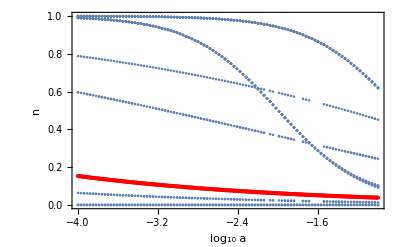

```mathematica
soln=Table[Select[Flatten[sol[[j]]],#[[1]]==n[1]||#[[1]]==n[2]||#[[1]]==n[3]||#[[1]]==n[4]||#[[1]]==n[5]&],{j,Length@sol}];
asl=Table[j,{j,-4,-1,.03}];
solnn=Table[{asl[[j]],#}&/@DeleteDuplicates[Values[soln[[j]]]],{j,Length@soln}];
plt1=ListPlot[Flatten[solnn,1],Frame->True,FrameLabel->{"log_10 a","n"}];
asll=Table[j,{j,-4,-1,.01}];
plt2=ListPlot[Table[{asll[[j]],homg[[j]]},{j,Length@homg}],PlotStyle->Red];
Show[plt1,plt2]
```

```mathematica
Export["dataexpa.txt",Flatten[solnn,1]]
```

dataexp.txt

### Figure S1

#### Figure S1 (a)

Run ‘ModelS1a’ in IEp

```mathematica
figureFn[frameout,-1]
```

#### Figure S1 (b)

Obtained from https://pmneila.github.io/jsexp/grayscott/ with appropriate parameters.

### Figure S4

#### Figure S4 (a)

```mathematica
n=8;
pts=Flatten[Table[{#/2.,3./(2Sqrt[3])i}&/@Range[-i,i,2],{i,0,n}],1];
Graphics[{EdgeForm[Gray],RGBColor[{242,242,242}/256],RegularPolygon[#,{1/Sqrt[3],Pi/2},6]&/@pts,Black,Point/@pts,Blue,Table[Circle[{0,0},i,{2Pi/6,4Pi/6}],{i,n}],Black,Table[Text[StringForm["R_(``)",i],{-i/2-1,3/(2Sqrt[3])i}],{i,0,n}],Red,{PointSize[.015],Point/@{pts[[-5]],pts[[-4]],pts[[-6]]}}}]
```

-Graphics-

#### Figure S4 (c-d)

```mathematica
n=10;nn=10;
ri=6474199;
pts=Flatten[Table[{#/2.,3./(2Sqrt[3])i}&/@Range[-i,i,2],{i,0,n}],1];
ptsn=DeleteDuplicates@Flatten[Table[Chop[RotationTransform[k Pi/3][#]&/@pts],{k,6}],1];
norma=AssociationThread[Norm[#]/n&/@ptsn,RandomSample[Norm[#]/n&/@ptsn]];
Graphics[{EdgeForm[Gray],{ColorData["LightTemperatureMap"][Floor[.999Norm[#]]/n],RegularPolygon[#,{1/Sqrt[3],Pi/2},6]}&/@ptsn}]
Graphics[{EdgeForm[Gray],{SeedRandom[ri+Floor[Norm[#]*10^5]];RandomColor[],RegularPolygon[#,{1/Sqrt[3],Pi/2},6]}&/@ptsn}]
```

#### Figure S4 (e-f)

```mathematica
n=39;nn=10;
ri=6474199;
pts=Flatten[Table[{#/2.,3./(2Sqrt[3])i}&/@Range[-i,i,2],{i,0,n}],1];
ptsn=DeleteDuplicates@Flatten[Table[Chop[RotationTransform[k Pi/3][#]&/@pts],{k,6}],1];
normsl=Sort@DeleteDuplicates[Round[Norm[#],.0000001]&/@ptsn];
norma=AssociationThread[normsl,Table[m=2;1.-Mod[j,m]/(m-1),{j,Length@normsl}]];
normsl2=Sort@DeleteDuplicates[Round[Floor[.999Norm[#]],.0000001]&/@ptsn];
norma2=AssociationThread[normsl2,Table[m=2;1.-Mod[j,m]/(m-1),{j,Length@normsl2}]];
Graphics[{EdgeForm[None],{ColorData["GrayTones"][1-norma2[Round[Floor[.999Norm[#]],.0000001]]],RegularPolygon[#,{1/Sqrt[3],Pi/2},6]}&/@ptsn}]
Graphics[{EdgeForm[None],{ColorData["GrayTones"][norma[Round[Norm[#],.0000001]]],RegularPolygon[#,{1/Sqrt[3],Pi/2},6]}&/@ptsn}]
```

### Figure S5

Run ‘ModelS5’ in IEp and generate multiple models with increasing epsilon (under Statistics). Run All.
Store the timing values with the following code.
Note: Sometimes, due to initial conditions, patterning might not be finished. To fix, tweak dTh (Delta threshold).

```mathematica
(* run for multiple simulations *)
sold=Table[Values[solsl[[i,j]]][[All,2]],{i,21},{j,100}];
inde=1;
Export[NotebookDirectory[]<>"\\InteractiveEpithelium\\Models\\epsilon\\"<>"12_"<>ToString@inde<>".txt",sold,"String"];
```

```mathematica
(* Plot saved data *)
findtime=Function[{data,dTh,dtV},
i0=20;
Table[FirstPosition[Table[Abs[Variance[data[[j,i]]]-Variance[data[[j,-1]]]]<dtV&&And@@(Abs[#]<dTh&/@(data[[j,i]]-data[[j,i-1]])),{i,i0,100}],True][[1]]+i0,{j,21}]];

epsll=Range[0,1,0.05];
timesll1={};timesll2={};timesll3={};
Quiet@Do[
data1=ToExpression@Import[NotebookDirectory[]<>"\\InteractiveEpithelium\\Models\\epsilon\\"<>"12_"<>ToString@indi<>".txt","List"][[1]];
AppendTo[timesll1,findtime[data1,0.05,0.02]];
data2=ToExpression@Import[NotebookDirectory[]<>"\\InteractiveEpithelium\\Models\\epsilon\\"<>"21_"<>ToString@indi<>".txt","List"][[1]];
AppendTo[timesll2,findtime[data2,0.03,0.01]]; (* adjust around ϵ = 0.5 *)
data3=ToExpression@Import[NotebookDirectory[]<>"\\InteractiveEpithelium\\Models\\epsilon\\"<>"513_"<>ToString@indi<>".txt","List"][[1]];
AppendTo[timesll3,findtime[data3,0.05,0.02]],
{indi,10}];
```

```mathematica
lpp1=Table[{epsll[[j]],(N@Mean@timesll1)[[j]]},{j,Length@epsll}];
lpp2=Table[{epsll[[j]],(N@Mean@timesll2)[[j]]},{j,Length@epsll}];
lpp3=Table[{epsll[[j]],(N@Mean@timesll3)[[j]]},{j,Length@epsll}];
interpf1=Interpolation[lpp1,InterpolationOrder->9];
interpf2=Interpolation[lpp2,InterpolationOrder->9];
interpf3=Interpolation[lpp3,InterpolationOrder->9];
Plot[{interpf1[x],interpf2[x],interpf3[x]},{x,0.,1},PlotRange->{{0,1},All},Frame->True,FrameLabel->{"ϵ","Patterning time"},PlotLegends->Placed[{"(10,10^2)","(10^2,10)","(10^5,10^1.3)"},{.82,.8}],PlotStyle->{Red,{Red,Dashed},{Red,Dotted}}]
```